```mathematica
eqn={y''[x]+4*y'[x]==8,y[0] == 0, y'[ 0 ] == 0}
```

{4 y'[x]+y''[x]==8,y[0]==0,y'[0]==0}

```mathematica
sol=Simplify[DSolve[eqn,y[x],x]]
```

{{y[x]→1/2 (-1+ⅇ^(-4 x)+4 x)}}

```mathematica
space=y[x]/.sol
velocity=Dt[y[x]/.sol,x]
```

{1/2 (-1+ⅇ^(-4 x)+4 x)}

{1/2 (4-4 ⅇ^(-4 x))}

```mathematica
{x-ⅇ^-x (1-ⅇ^x+ⅇ^x x)}
```

{x-ⅇ^-x (1-ⅇ^x+ⅇ^x x)}

```mathematica
acceleration=Dt[velocity,x]
```

{8 ⅇ^(-4 x)}

1.

0.05

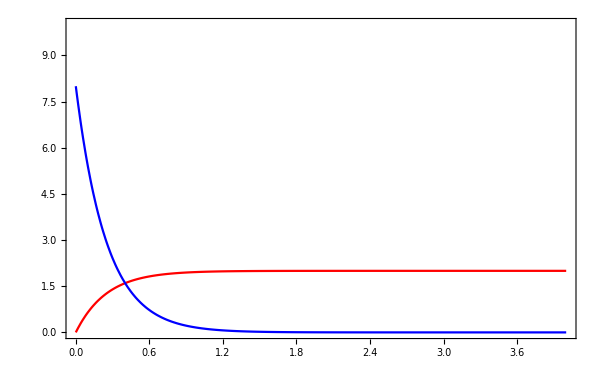

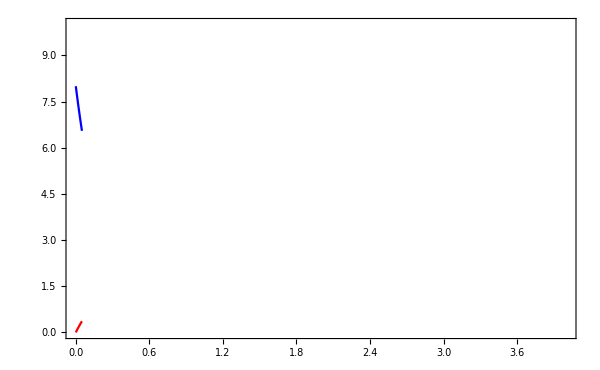
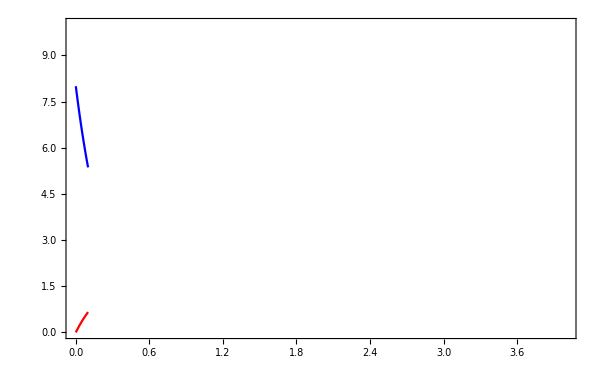
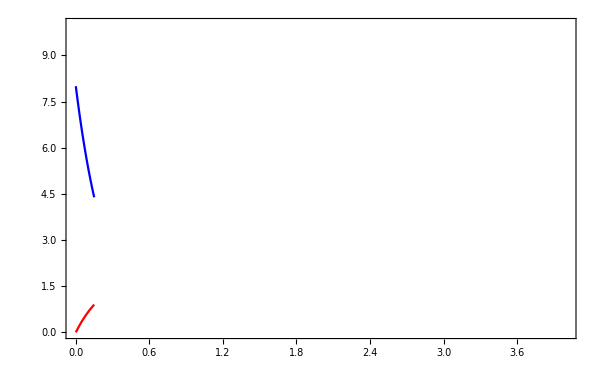
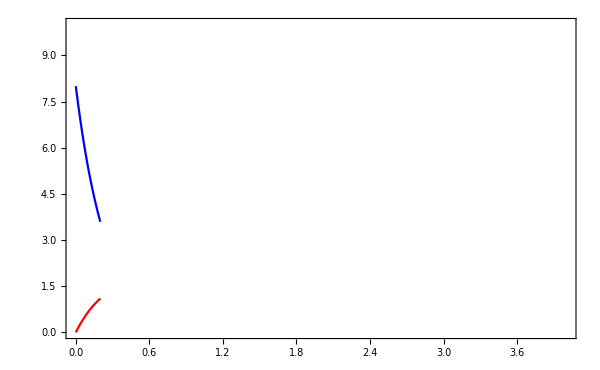
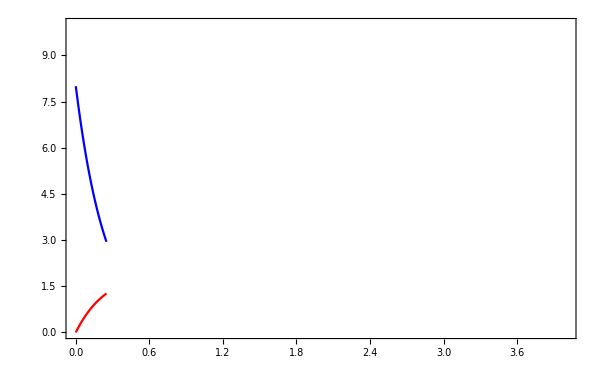
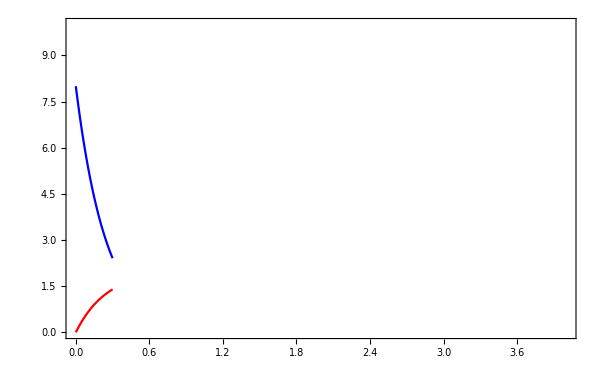
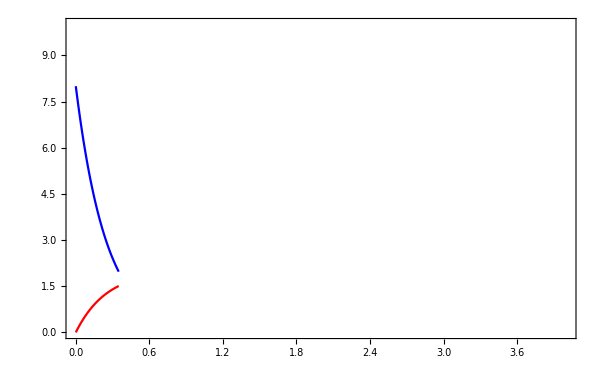

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
intermediateTime=1.
animationStep=0.05
plot=Plot[Evaluate[{velocity,acceleration}],{x,0,4}, ImageSize->600,Frame->True,Axes->False,PlotRange->{{0,4},{0,10}},LabelStyle->Opacity[0],PlotStyle->{{Red,Dashing[None]},{Blue,Dashing[None]}}]
plotsStep1=Table[Plot[Evaluate[{velocity,acceleration}],{x,0,i}, ImageSize->600,Frame->True,Axes->False,PlotRange->{{0,4},{0,10}},LabelStyle->Opacity[0],PlotStyle->{{Red,Dashing[None]},{Blue,Dashing[None]}}],{i,animationStep,intermediateTime,animationStep}]
plotsStep2=Table[Plot[Evaluate[{velocity,acceleration}],{x,0,i}, ImageSize->600,Frame->True,Axes->False,PlotRange->{{0,4},{0,10}},LabelStyle->Opacity[0],PlotStyle->{{Red,Dashing[None]},{Blue,Dashing[None]}}],{i,intermediateTime,4,animationStep*3/2}]
```

```mathematica
Export["/Users/meridian/Documents/StokesODE_animation_step1.mov",plotsStep1]
```

/Users/meridian/Documents/StokesODE_animation_step1.mov

```mathematica
Export["/Users/meridian/Documents/StokesODE_animation_step1.gif",plotsStep1]
```

/Users/meridian/Documents/StokesODE_animation_step1.gif

```mathematica
Export["/Users/meridian/Documents/StokesODE_animation_step2.mov",plotsStep2]
```

/Users/meridian/Documents/StokesODE_animation_step2.mov

```mathematica
Export["/Users/meridian/Documents/StokesODE_animation_step2.gif",plotsStep2]
```

/Users/meridian/Documents/StokesODE_animation_step2.gif

```mathematica
Export["/Users/meridian/Documents/StokesODE.png",plot]
```

/Users/meridian/Documents/StokesODE.png